# Homework 11

Name: Eslam Muhammed Ahmed Zenhom

ID: 201700788

## Problem 1

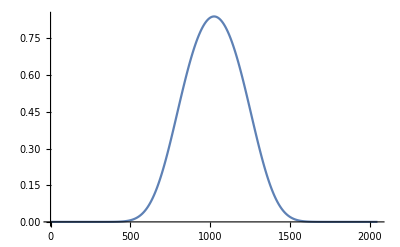

{0.667985,2.39363,4.69676,7.33565,10.2442,13.3791,16.7115,20.2202,23.8892,27.7053}

Ground state energy:

0.667985

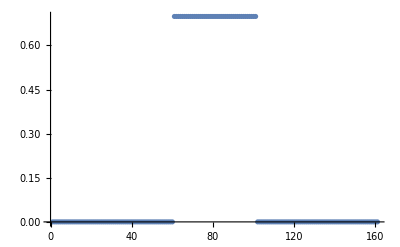

0.678974

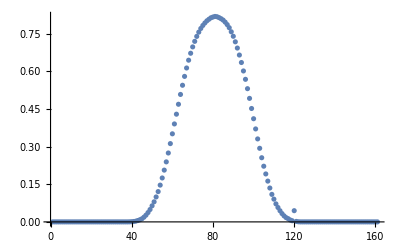

```mathematica
(*Matrix Method*)
ClearAll["Global`*"]
dr =2.0^-8;
r = Range[-4,4,dr];
lr = Length[r];
pot = r^4;
d1 =-1.0/(2.0 dr^2);
d2 = 1.0/(dr^2);
hmat = Array[0 &, {lr,lr}];
hmat[[1,1]] = pot[[1]] + d2;
hmat[[1,2]] =  d1;
hmat[[lr,lr]] = pot[[lr]] + d2;
hmat[[lr,lr-1]] =  d1;
Do[
hmat[[i,i-1]] = d1;hmat[[i,i+1]] = d1;hmat[[i,i]] = pot[[i]] + d2,
{i,2,lr-1}]
hmat;
psi1=Sort[Eigensystem[hmat]][[2,-1]];
psi2=psi1/(√(psi1.psi1 dr));
ListPlot[psi2, Joined->True]

en =Sort[Eigenvalues[hmat]];
en[[1;;10]]
Print["Ground state energy:"]
Min[en] (*Ground state energy*)

(*varitional method*)
ClearAll["Global`*"]
dx = 0.05; xMin = -4;xMax = 4; 
x = Range[xMin,xMax,dx]; lx = Length[x];
phi = Table[0.0,{i,lx}];
Do[
If[x[[i]]>= -1.0 && x[[i]]<= 1.0, phi[[i]] = 0.50]
,{i,lx}];
phi = phi/(√(phi.phi dx)); (* normalization *)

ListPlot[phi]
vLJ[x_]:= x^4;
pot = vLJ[x]; (* the potential *)
hmat = Array[0 &, {lx,lx}];
d2 = 1.0/dx^2;
d1 = -0.50/dx^2;
hmat[[1,1]] = pot[[1]] + d2;
hmat[[1,2]] =  d1;
hmat[[lx,lx]] = pot[[lx]] + d2;
hmat[[lx,lx-1]] =  d1;
Do[
hmat[[i,i-1]] = d1;hmat[[i,i+1]] = d1;hmat[[i,i]] = pot[[i]] + d2,
{i,2,lx-1}]
hmat//MatrixForm;

engOld = dx phi.hmat.phi;

Do[
nRan =RandomInteger[{1,lx}];
phiTry = phi;
phiTry[[nRan]] = phiTry[[nRan]]+ RandomReal[{-0.2,0.2}];
phiTry = phiTry/(√(phiTry.phiTry dx));
engNew =dx phiTry.hmat.phiTry; 
If[engNew < engOld,phi =phiTry; engOld = engNew],
{j,1000000}]
engOld
ListPlot[phiTry] (* dividing by Sqrt[dx] to get the right normalization *)
```

## Problem 2: Fig 10.14

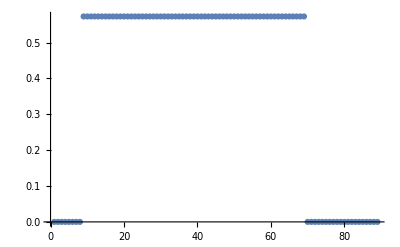

-0.904465

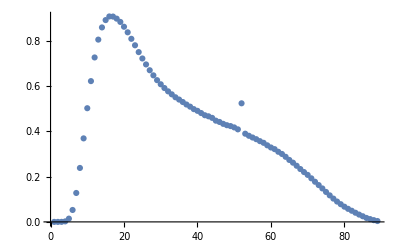

```mathematica
(*The varitional method*)

ClearAll["Global`*"]
dx = 0.05; xMin = 0.6;xMax = 5.0; 
x = Range[xMin,xMax,dx]; lx = Length[x];
phi = Table[0.0,{i,lx}];
Do[
If[x[[i]]>= 1.0 && x[[i]]<= 4.0, phi[[i]] = 0.50]
,{i,lx}];
phi = phi/(√(phi.phi dx)); (* normalization *)

ListPlot[phi]
vLJ[x_,ϵ_,σ_]:= 4 ϵ ((σ/x)^12-(σ/x)^6);
pot = vLJ[x,8.0,1.0]; (* Discrete potential *)
hmat = Array[0 &, {lx,lx}];
d2 = 1.0/dx^2;
d1 = -0.50/dx^2;
hmat[[1,1]] = pot[[1]] + d2;
hmat[[1,2]] =  d1;
hmat[[lx,lx]] = pot[[lx]] + d2;
hmat[[lx,lx-1]] =  d1;
Do[
hmat[[i,i-1]] = d1;hmat[[i,i+1]] = d1;hmat[[i,i]] = pot[[i]] + d2,
{i,2,lx-1}]
hmat//MatrixForm;

engOld = dx phi.hmat.phi;

Do[
nRan =RandomInteger[{1,lx}];
phiTry = phi;
phiTry[[nRan]] = phiTry[[nRan]]+ RandomReal[{-0.2,0.2}];
phiTry = phiTry/(√(phiTry.phiTry dx));
engNew =dx phiTry.hmat.phiTry; 
If[engNew < engOld,phi =phiTry; engOld = engNew],
{j,1000000}]
engOld
ListPlot[phiTry] (* dividing by Sqrt[dx] to get the right normalization *)
```

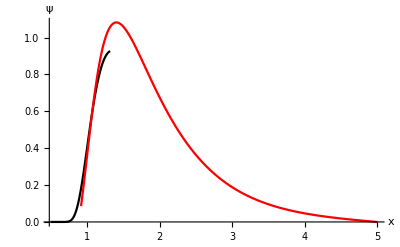

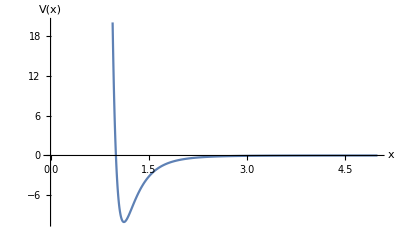

```mathematica
(*The matching method*)
dx = 0.01; xMin = 0.5;xMax = 5.0; 
x = Range[xMin,xMax,dx]; lx = Length[x];
eng =-0.9; (* first guess for E *)

dE = .04; (* first guess for dE *) 

vLJ[x_,ϵ_,σ_]:= 4 ϵ ((σ/x)^12-(σ/x)^6);
v = vLJ[x,8.0,1.0]; (* Discrete potential *)
iMin = Position[v,Min[v]][[1,1]]; (* Minimum potential position *)

iOverLap = 20; (* determines number of overlapping steps *)
(* Initialization of ψL and ψR;
ψL runs from the beginging of x to iOverLap steps beyond the minimum position of the potential; 
ψR runs iOverLap steps before the minimum till the end;
 ψL and ψR overlaps on 2 × iOverLap points on the x axis;
 *)
psiL = Table[0.0, {i,iMin + iOverLap}]; 
lL = Length[psiL];
psiR = Table[0.0, {i,iMin - iOverLap,lx}]; 
lR = Length[psiR];

(* Start with a small slope by giving the following values to the first elements in each psi. We keep the second elements zeros. So we start from the third elements *)
psiL[[1]] = -0.0001 dx; psiR[[1]] =psiL[[1]]; 

(* Obtaining the slopes of the initial psi *)
Do[psiL[[i]] = 2.0 psiL[[i-1]] - psiL[[i-2]] - 2.0 (eng - v[[i-1]])psiL[[i-1]] dx^2  
,{i,3,lL}];
Do[psiR[[i]] = 2.0 psiR[[i-1]] - psiR[[i-2]] - 2.0 (eng - v[[1-i]])psiR[[i-1]] dx^2  
,{i,3,lR}]; (* v is reversed: not i - 1, but -(i - 1) *)
psiR = Reverse[psiR]; (* reverse the elements of ψR to the right order *)

psiR = psiR/(√(psiR.psiR *dx)); (*the normalization*)
(* Scaling: ψL = ψR at the minimum position of v *)
psiL = psiL psiR[[iOverLap]]/psiL[[iMin]]; 

(* Slopes calculations: Slope ≡ difference, since dx is the same *)
sL = psiL[[iMin+1]] -  psiL[[iMin-1]];
sR = psiR[[iOverLap+1]] -  psiR[[iOverLap-1]];
xpsiL = Table[{x[[i]], psiL[[i]]},{i,lL}];
xpsiR = Table[{x[[i+lx-lR]], psiR[[i]]},{i,lR}]; 
p1 = ListPlot[xpsiL, PlotStyle->Black, Joined->True];  p2 = ListPlot[xpsiR,PlotStyle->Red, Joined->True]; 
Show[p1,p2,PlotRange-> All,AxesLabel-> {"x","ψ"}]
Plot[vLJ[x,10.0,1.0],{x,0.5,5}, PlotRange->{{-10,20}},AxesLabel->{"x","V(x)"}]
```

## Problem 3

## Problem 4

## Problem 5

## Problem 6

## Problem 7

## Problem 8

## Problem 9

## Problem 10